```mathematica
Quit[]
(*Classical benchmark*)
```

```mathematica
(*Computation of symplectic spectra/matrices for inputs given by either: CovH0, CovH1gen, CovH1ent*)

SymY[x_]:=(x[[1,1]]+x[[4,4]])^2 - 4 (x[[1,3]])^2;

SymEigPlus[x_]:=(Sqrt[SymY[x]] + (x[[4,4]]-x[[1,1]]))/2;
SymEigMinus[x_]:=(Sqrt[SymY[x]] - (x[[4,4]]-x[[1,1]]))/2;

SymCov[x_]:= List[SymEigMinus[x],SymEigMinus[x],SymEigPlus[x],SymEigPlus[x]];

SymOmegaPlus[x_]:=Sqrt[(x[[1,1]]+x[[4,4]] + Sqrt[SymY[x]])/(2Sqrt[SymY[x]])];
SymOmegaMinus[x_]:=Sqrt[(x[[1,1]]+x[[4,4]] - Sqrt[SymY[x]])/(2Sqrt[SymY[x]])];

SymMat[x_]:=ArrayFlatten[{{SymOmegaPlus[x]IdentityMatrix[2],SymOmegaMinus[x]PauliMatrix[3]},{SymOmegaMinus[x]PauliMatrix[3],SymOmegaPlus[x]IdentityMatrix[2]}}];

(*Computation of Chernoff bound for distinguising between cases: i) CovH0 and CovH1gen; and ii) CovH0 and CovH1ent*)

G[x_]:=DiagonalMatrix[(2^(1/2))/((x+1)^(1/2)-(x-1)^(1/2))];
L[x_]:=DiagonalMatrix[((x+1)^(1/2)+(x-1)^(1/2))/((x+1)^(1/2)-(x-1)^(1/2))];
d[d0_,d1_]:=d1-d0;
ChernPi[x0_,x1_]:= G[SymCov[x0]] . G[SymCov[x1]];
ChernSigma[x0_,x1_]:= SymMat[x0] .  L[SymCov[x0]] . Transpose[SymMat[x0]] +   SymMat[x1] .  L[SymCov[x1]].Transpose[SymMat[x1]];
Chern[x0_,x1_,d0_,d1_,N_] := (2^N)Sqrt[(Det[ChernPi[x0,x1]])/(Det[ChernSigma[x0,x1]])] Exp[-(d[d0,d1].MatrixPower[ChernSigma[x0,x1],-1].Transpose[d[d0,d1]])/2];

SymCovCS[x_]:= List[x[[1,1]],x[[2,2]]];

ChernPiCS[x0_,x1_]:=  G[SymCovCS[x0]] . G[SymCovCS[x1]];
ChernSigmaCS[x0_,x1_]:= IdentityMatrix[2] .  L[SymCovCS[x0]] . Transpose[IdentityMatrix[2]] +   IdentityMatrix[2] .  L[SymCovCS[x1]].Transpose[IdentityMatrix[2]];
ChernCS[x0_,x1_,d0_,d1_,N_] := (2^N)Sqrt[(Det[ChernPiCS[x0,x1]])/(Det[ChernSigmaCS[x0,x1]])] Exp[-(d[d0,d1].MatrixPower[ChernSigmaCS[x0,x1],-1].Transpose[d[d0,d1]])/2];
```

```mathematica
$Assumptions=Ns>0 && Nb>0 && Na>0 && k>0 && Z>0 && Element[Ns,Reals] && Element[Nb,Reals]&& Element[Na,Reals] && Element[k,Reals] && Element[Z,Reals] &&Ns≠0 &&Nb≠0 &&k≠0 &&Z≠0;
(*Building Covariance matrixes for the cases of target absent (CovH0), and a target present for: i) generic input source whose signal-idler quadrature correlations are quantified by term Z (CovH1gen); ii) input source whose signal-idler modes' quadratures are maximally entangled such that Z=Zent=2Sqrt[Ns(Ns+1)] (CovH1ent)*)
Ns=.; (*Number photons per mode for source*)
Nb=.; (*Number photons per mode for background*)
k=.; (*Reflectivity*)

(*Covariance matrices for QI*)
S = 2 Ns + 1;
B = 2 Nb + 1;
A = 2 k Ns +B;

Z=.;
Zent=.;
Zent=2Sqrt[Ns(Ns+1)];

CovH0=.;
CovH1gen=.;
CovH1ent=.;
CovH0 =DiagonalMatrix[{B,B,S,S}] ;
CovH1gen ={{A, 0, Sqrt[k]Z, 0}, {0,A, 0, -Sqrt[k]Z}, 
{Sqrt[k]Z, 0, S,0},{ 0, -Sqrt[k]Z, 0, S}};
CovH1ent ={{A, 0, Sqrt[k]Zent, 0}, {0,A, 0, -Sqrt[k]Zent}, 
{Sqrt[k]Zent, 0, S,0},{ 0, -Sqrt[k]Zent, 0, S}};
Meangen={{0,0,0,0}};

Aamp=2 k (Ns + Nas)+ B;
Samp = 2Ns + 2Nai +1;
CovH0entamp ={{B, 0, 0, 0}, {0,B, 0, 0}, 
{0, 0, Samp,0},{ 0, 0, 0, Samp}};
CovH1entamp ={{Aamp, 0, Sqrt[k]Zent, 0}, {0,Aamp, 0, -Sqrt[k]Zent}, 
{Sqrt[k]Zent, 0, Samp,0},{ 0, -Sqrt[k]Zent, 0, Samp}};
Meangen={{0,0,0,0}};
```

```mathematica
(*Covariance matrices for coherent states + amplifier*)
X = 2 Nb + 1;
Y = 2 k Na +X;

CSH0 =DiagonalMatrix[{X,X}] ;
CSH1 ={{Y, 0}, { 0, Y}};
CSmean0={{0,0}};
CSmean1={{2Sqrt[k Ns],0}};

(**Coherent states made at room temperature then passed through fridge*)
Z=2 Nb + 2k Ne +1;
CSH12={{Z,0},{0,Z}};
CSmean12={{2 Sqrt[k  f Ns ],0}};
```

```mathematica
Vsi={{2Ns+1,0,2Sqrt[Ns(Ns+1)],0},{0, 2Ns+1, 0, - 2Sqrt[2Ns+1]},{2Sqrt[Ns(Ns+1)],0,2Ns+1,0},{0,-2Sqrt[Ns[Ns+1]],0,2Ns+1}}//MatrixForm
```

(1+2 Ns | 0 | 2 √(Ns (1+Ns)) | 0
0 | 1+2 Ns | 0 | -2 √(1+2 Ns)
2 √(Ns (1+Ns)) | 0 | 1+2 Ns | 0
0 | -2 √Ns[1+Ns] | 0 | 1+2 Ns)

```mathematica
(*TMSV + Amp QCB*)
Chern[CovH0entamp,CovH1entamp,Meangen,Meangen,2]
```

```mathematica
TMSVampQCB[Ns_,Nb_,k_,Nas_, Nai_]:=16 √(1/((-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2))))^2 (-√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2))))^2 (-√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))))^2 (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))))^2 ((((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))) (((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))) ((((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))) (((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))))))-(((√((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) √((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+(√((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) √((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) (√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 (-√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+(√((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) √((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) (√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 (-√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))+(√((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) √((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))))^2)-((-((√((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) √((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2))))))-(√((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) √((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) (√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 (-√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))-(√((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) √((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) (√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 (-√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))-(√((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) √((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))))^2 ((((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))) (((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 √((2+2 Nai+2 Nb+2 Ns)^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))+((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 √(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2) (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))))))-(((√((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) √((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+(√((2+2 Nai+2 Nb+2 Ns-√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) √((2+2 Nai+2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2))/(√((2+2 Nai+2 Nb+2 Ns)^2))) (√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))/(2 (-√(-1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns+√((2+2 Nai+2 Nb+2 Ns)^2)))))+(√((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) √((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) (√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 (-√(-1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (2 Nai-2 Nb+2 Ns-2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))+(√((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)-√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) √((2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))/(√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2))) (√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))/(2 (-√(-1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))+√(1+1/2 (-2 Nai+2 Nb-2 Ns+2 k (Nas+Ns)+√(-16 k Ns (1+Ns)+(2+2 Nai+2 Nb+2 Ns+2 k (Nas+Ns))^2)))))))^2))));
```

```mathematica
(*Coherent state QCB*)

ChernCS[CSH0,CSH0,CSmean0,CSmean1,1]
```

{{4 ⅇ^(-(k (-√2 √Nb+√(2+2 Nb)) Ns)/(√2 √Nb+√(2+2 Nb))) √(1/((-√2 √Nb+√(2+2 Nb))^4 (8/(-√2 √Nb+√(2+2 Nb))^2+(16 Nb)/(-√2 √Nb+√(2+2 Nb))^2+(8 √2 √Nb √(2+2 Nb))/(-√2 √Nb+√(2+2 Nb))^2)))}}

```mathematica
FullSimplify[4 ⅇ^(-(k (-√2 √Nb+√(2+2 Nb)) Ns)/(√2 √Nb+√(2+2 Nb))) √(1/((-√2 √Nb+√(2+2 Nb))^4 (8/(-√2 √Nb+√(2+2 Nb))^2+(16 Nb)/(-√2 √Nb+√(2+2 Nb))^2+(8 √2 √Nb √(2+2 Nb))/(-√2 √Nb+√(2+2 Nb))^2)))]
```

ⅇ^(k (-1-2 Nb+2 √(Nb (1+Nb))) Ns)

```mathematica
Series[ⅇ^(k (-1-2 Nb+2 √(Nb (1+Nb))) Ns),{Nb,Infinity,1}]
```

1-(k Ns)/(4 Nb)+O[1/Nb]^2

```mathematica
(*Coherent state + amplifier QCB*)
ChernCS[CSH0,CSH1,CSmean0,CSmean1,1]
```

{{4 ⅇ^(-(2 k Ns)/((√2 √Nb+√(2+2 Nb))/(-√2 √Nb+√(2+2 Nb))+(√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))/(-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb)))) √(1/((-√2 √Nb+√(2+2 Nb))^2 (-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))^2 (2/(-√2 √Nb+√(2+2 Nb))^2+(4 Nb)/(-√2 √Nb+√(2+2 Nb))^2+(2 √2 √Nb √(2+2 Nb))/(-√2 √Nb+√(2+2 Nb))^2+2/(-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))^2+(4 k Na)/(-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))^2+(4 Nb)/(-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))^2+(2 √(2 k Na+2 Nb) √(2+2 k Na+2 Nb))/(-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))^2+(2 √2 √Nb √(2 k Na+2 Nb))/((-√2 √Nb+√(2+2 Nb)) (-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb)))+(2 √(2+2 Nb) √(2 k Na+2 Nb))/((-√2 √Nb+√(2+2 Nb)) (-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb)))+(2 √2 √Nb √(2+2 k Na+2 Nb))/((-√2 √Nb+√(2+2 Nb)) (-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb)))+(2 √(2+2 Nb) √(2+2 k Na+2 Nb))/((-√2 √Nb+√(2+2 Nb)) (-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))))))}}

```mathematica
FullSimplify[4 ⅇ^(-(2 k Ns)/((√2 √Nb+√(2+2 Nb))/(-√2 √Nb+√(2+2 Nb))+(√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))/(-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb)))) √(1/((-√2 √Nb+√(2+2 Nb))^2 (-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))^2 (2/(-√2 √Nb+√(2+2 Nb))^2+(4 Nb)/(-√2 √Nb+√(2+2 Nb))^2+(2 √2 √Nb √(2+2 Nb))/(-√2 √Nb+√(2+2 Nb))^2+2/(-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))^2+(4 k Na)/(-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))^2+(4 Nb)/(-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))^2+(2 √(2 k Na+2 Nb) √(2+2 k Na+2 Nb))/(-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))^2+(2 √2 √Nb √(2 k Na+2 Nb))/((-√2 √Nb+√(2+2 Nb)) (-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb)))+(2 √(2+2 Nb) √(2 k Na+2 Nb))/((-√2 √Nb+√(2+2 Nb)) (-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb)))+(2 √2 √Nb √(2+2 k Na+2 Nb))/((-√2 √Nb+√(2+2 Nb)) (-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb)))+(2 √(2+2 Nb) √(2+2 k Na+2 Nb))/((-√2 √Nb+√(2+2 Nb)) (-√(2 k Na+2 Nb)+√(2+2 k Na+2 Nb))))))]
```

ⅇ^((k (√Nb-√(1+Nb)) (√(k Na+Nb)-√(1+k Na+Nb)) Ns)/(√(Nb (k Na+Nb))-√((1+Nb) (1+k Na+Nb))))/(√(1+2 Nb (1+Nb)-2 √(Nb (1+Nb) (k Na+Nb) (1+k Na+Nb))+k (Na+2 Na Nb)))

```mathematica
AmpChern=ⅇ^((k (√Nb-√(1+Nb)) (√(k Na+Nb)-√(1+k Na+Nb)) Ns)/(√(Nb (k Na+Nb))-√((1+Nb) (1+k Na+Nb))))/(√(1+2 Nb (1+Nb)-2 √(Nb (1+Nb) (k Na+Nb) (1+k Na+Nb))+k (Na+2 Na Nb)));
```

```mathematica
AmpChern/.Na-> 0
```

(ⅇ^((k (√Nb-√(1+Nb))^2 Ns)/(√(Nb^2)-√((1+Nb)^2))))/(√(1+2 Nb (1+Nb)-2 √(Nb^2 (1+Nb)^2)))

```mathematica
Series[AmpChern,{Nb,Infinity,1}]
Series[AmpChern,{Na,0,1}]
FullSimplify[Series[AmpChern,{Na,Infinity,1}]]
```

1-(k Ns)/(4 Nb)+O[1/Nb]^2

ⅇ^(-k (-√Nb+√(1+Nb))^2 Ns)+(ⅇ^(-k (-√Nb+√(1+Nb))^2 Ns) k^2 (-√Nb+√(1+Nb))^2 Ns Na)/(2 √Nb √(1+Nb))+O[Na]^2

(√(1/Na))/(√(k (1+2 Nb-2 √(Nb+Nb^2))))+O[1/Na]^(3/2)

```mathematica
(*Recovers CD QCB for Na -> 0*)
FullSimplify[(ⅇ^((k (√Nb-√(1+Nb)) (√(k Na+Nb)-√(1+k Na+Nb)) Ns)/(√(Nb (k Na+Nb))-√((1+Nb) (1+k Na+Nb))))/(√(1+2 Nb (1+Nb)-2 √(Nb (1+Nb) (k Na+Nb) (1+k Na+Nb))+k (Na+2 Na Nb))))/.Na-> 0]
```

ⅇ^(k (-1-2 Nb+2 √(Nb (1+Nb))) Ns)

```mathematica
(*Optical coherent state benchmark*)
```

```mathematica
CSChern=ⅇ^(k (-1-2 Nb+2 √(Nb (1+Nb))) Ns);
```

```mathematica
(*Coherent state - source generated at room temp (RT) + attenuation at temp T - added noise Ne *)
h=6.62606957 10^-34;
kb=1.3806488 10^-23;
c=299792458;
Ne=1/(Exp[(h v)/(kb T )]-1);
```

```mathematica
RTChern=ⅇ^((f k (√Nb-√(1+Nb)) (√(Nb+k Ne)-√(1+Nb+k Ne)) Ns)/(√(Nb (Nb+k Ne))-√((1+Nb) (1+Nb+k Ne)))) √(1/(1+k Ne+2 Nb (1+Nb+k Ne)-2 √(Nb (1+Nb) (Nb+k Ne) (1+Nb+k Ne))));
```

```mathematica
(*PLOTS*)
```

```mathematica
NbNUM=6250;
NaNUM2=6250;
NaNUM3=5 10^8;
```

```mathematica
GraphicsColumn[{Plot[{(1/2)AmpChern^(10^M)/.{Nb-> NbNUM,k-> 1/100,Ns-> 1/100,Na-> NaNUM2},(1/2)RTChern^(10^M)/.{k->1/100,Ns-> (1/100+NaNUM2-Ne)/f,f-> 1/100}/.{v-> 10^9,Nb-> NbNUM,T-> 300,f-> 1/100},(1/2)RTChern^(10^M)/.{k->1/100,Ns-> (1/100+NaNUM2-Ne)/f,f-> 1/100}/.{v-> 10^9,Nb-> NbNUM,T-> 100,f-> 1/100},(1/2)RTChern^(10^M)/.{k->1/100,Ns-> (1/100+NaNUM2-Ne)/f,f-> 1/100}/.{v-> 10^9,Nb-> NbNUM,T-> 10,f-> 1/100},(1/2)CSChern^(10^M)/.{Nb-> NbNUM,k-> 1/100,Ns-> 1/100+NaNUM2}},{M,0,6},PlotLegends->Placed[{"CS+Amp","CS+RT1","CS+RT2","CS+RT3","CS"},{0.85,0.7}],PlotStyle->{Orange,{Darker[Pink],Dashed},Darker[Green],Lighter[Blue],Purple},Frame->True,FrameLabel->{"Log_10(M)","P_err"}],
Plot[{(1/2)AmpChern^(10^M)/.{Nb-> NbNUM,k-> 1/10000000,Ns-> 1/100,Na-> NaNUM3},(1/2)RTChern^(10^M)/.{k->1/10000000,Ns-> (1/100+NaNUM3-Ne)/f,f-> 1/100}/.{v-> 10^9,Nb-> NbNUM,T-> 300,f-> 1/100},(1/2)RTChern^(10^M)/.{k->1/10000000,Ns-> (1/100+NaNUM3-Ne)/f,f-> 1/100}/.{v-> 10^9,Nb-> NbNUM,T-> 100,f-> 1/100},(1/2)RTChern^(10^M)/.{k->1/10000000,Ns-> (1/100+NaNUM3-Ne)/f,f-> 1/100}/.{v-> 10^9,Nb-> NbNUM,T-> 10,f-> 1/100},(1/2)CSChern^(10^M)/.{Nb-> NbNUM,k-> 1/10000000,Ns-> 1/100+NaNUM3}},{M,0,6},PlotLegends->Placed[{"CS+Amp","CS+RT1","CS+RT2","CS+RT3","CS"},{0.85,0.7}],PlotStyle->{Orange,{Darker[Pink],Dashed},Darker[Green],Lighter[Blue],Purple},Frame->True,FrameLabel->{"Log_10(M)","P_err"}]}]
```

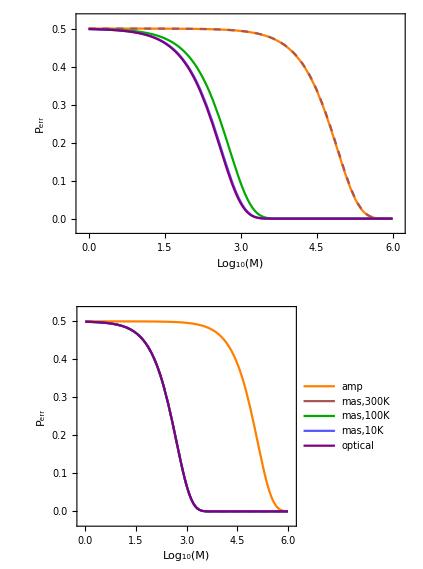

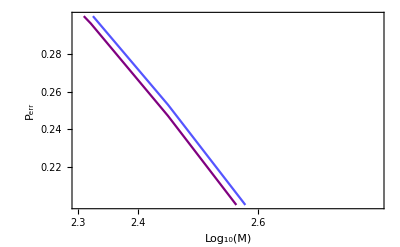

```mathematica
Plot[{(1/2)RTChern^(10^M)/.{k->1/100,Ns-> (1/100+NaNUM2-Ne)/f,f-> 1/100}/.{v-> 10^9,Nb-> NbNUM,T-> 10,f-> 1/100},(1/2)CSChern^(10^M)/.{Nb-> NbNUM,k-> 1/100,Ns-> 1/100+NaNUM2}},{M,0,6},PlotRange-> {{2.3,2.6},{0.2,0.3}},PlotStyle->{Lighter[Blue],Purple},Frame->True,FrameLabel->{"Log_10(M)","P_err"},FrameTicks->{{{0.22,0.24,0.26,0.28},{None}},{{2.3,2.4,2.6},{None}}}]
```

```mathematica
(*QRE and QREV*)
```

```mathematica
(*Covariance matrices for coherent states + amplifier and fridge*)
Xhalf = Nb + 1/2;
Yhalf = k Na +Xhalf;
Zhalf=Nb + k Nt +1/2;

CSH0half =DiagonalMatrix[{Xhalf,Xhalf}] ;
CSH1half ={{Yhalf, 0}, { 0, Yhalf}};
CSH12half={{Zhalf,0},{0,Zhalf}};
CSmean0half={{0,0}};
CSmean1half={{Sqrt[2 k Ns],0}};
CSmean12half={{ Sqrt[2 k  f Ns ],0}};

omegasymp = {{0,1},{-1,0}};
```

```mathematica
dhalf[d0_,d1_]:=d1-d0;
Argument[x_]:=2I (x . omegasymp);
G[x_]:= 2I (omegasymp . MatrixFunction[ArcCoth,Argument[x]]);
Sigma[x0_,x1_,d0_,d1_]:=( Log[Det[x1 + (I omegasymp /2)]] + Tr[x0 . G[x1]]+ dhalf[d0,d1].G[x1].Transpose[dhalf[d0,d1]])/2;
GamFun[x0_,x1_]:=G[x0]-G[x1];
```

```mathematica
RelEnt[x0_,x1_,d0_,d1_]:= -Sigma[x0,x0,d0,d0] + Sigma[x0,x1,d0,d1];
RelEntVar[x0_,x1_,d0_,d1_]:= (1/2)Tr[MatrixPower[GamFun[x0,x1].x0,2]] + (1/8) Tr[MatrixPower[GamFun[x0,x1].omegasymp,2]] + dhalf[d0,d1].G[x1].x0.G[x1].Transpose[dhalf[d0,d1]] ;
```

```mathematica
FullSimplify[RelEnt[CSH0half,CSH0half,CSmean0half,CSmean1half][[1,1]]]
```

```mathematica
RelEntCS[Ns_,Nb_,k_]:=2 k Ns ArcCoth[1+2 Nb]
```

```mathematica
Series[2 k Ns ArcCoth[1+2 Nb],{Nb,Infinity,1}]
```

(k Ns)/Nb+O[1/Nb]^2

```mathematica
FullSimplify[RelEntVar[CSH0half,CSH0half,CSmean0half,CSmean1half][[1,1]]]
```

```mathematica
RelEntVarCS[Ns_,Nb_,k_]:=4 k (1+2 Nb) Ns ArcCoth[1+2 Nb]^2
```

```mathematica
Series[4 k (1+2 Nb) Ns ArcCoth[1+2 Nb]^2,{Nb,Infinity,1}]
```

(2 k Ns)/Nb+O[1/Nb]^2

```mathematica
FullSimplify[RelEnt[CSH0half,CSH12half,CSmean0half,CSmean12half][[1,1]]]
```

```mathematica
RelEntRT[Ns_,Nb_,k_,Nt_,f_]:=1/2 (-2 (1+2 Nb) ArcCoth[1+2 Nb]+(2+4 Nb+4 f k Ns) ArcCoth[1+2 Nb+2 k Nt]-Log[Nb (1+Nb)]+Log[(Nb+k Nt) (1+Nb+k Nt)])
```

```mathematica
FullSimplify[RelEntVar[CSH0half,CSH12half,CSmean0half,CSmean12half][[1,1]]]
```

```mathematica
RelEntVarRT[Ns_,Nb_,k_,Nt_,f_]:=4 Nb (1+Nb) ArcCoth[1+2 Nb]^2-8 Nb (1+Nb) ArcCoth[1+2 Nb] ArcCoth[1+2 Nb+2 k Nt]+4 (Nb+Nb^2+f k Ns+2 f k Nb Ns) ArcCoth[1+2 Nb+2 k Nt]^2
```

```mathematica
FullSimplify[RelEnt[CSH0half,CSH1half,CSmean0half,CSmean1half][[1,1]]]
```

```mathematica
RelEntAmp[Ns_,Nb_,k_,Na_]:=1/2 (-2 (1+2 Nb) ArcCoth[1+2 Nb]+(2+4 Nb+4 k Ns) ArcCoth[1+2 k Na+2 Nb]-Log[Nb (1+Nb)]+Log[(k Na+Nb) (1+k Na+Nb)])
```

```mathematica
Series[1/2 (-2 (1+2 Nb) ArcCoth[1+2 Nb]+(2+4 Nb+4 k Ns) ArcCoth[1+2 k Na+2 Nb]-Log[Nb (1+Nb)]+Log[(k Na+Nb) (1+k Na+Nb)]),{Nb,Infinity,1}]
```

(k Ns)/Nb+O[1/Nb]^2

```mathematica
FullSimplify[RelEntAmp[Ns,Nb,k,Na]-((1/2)((1+2 Nb + 2 k Ns)Log[1 + (1/(k Na + Nb))] - (1 + 2Nb) Log[1 + (1/Nb)] + Log[(k Na + Nb)(1 + k Na + Nb)/(Nb (1+Nb))]))/.{Ns-> 1,Nb-> 500,k-> 0,Na-> 100}]
```

0

```mathematica
FullSimplify[RelEntVar[CSH0half,CSH1half,CSmean0half,CSmean1half][[1,1]]]
```

```mathematica
RelEntVarAmp[Ns_,Nb_,k_,Na_]:=4 Nb (1+Nb) ArcCoth[1+2 Nb]^2-8 Nb (1+Nb) ArcCoth[1+2 Nb] ArcCoth[1+2 k Na+2 Nb]+4 (Nb+Nb^2+k Ns+2 k Nb Ns) ArcCoth[1+2 k Na+2 Nb]^2
```

```mathematica
RelEntAmp[Ns,Nb,k,0]
RelEntVarAmp[Ns,Nb,k,0]
```

1/2 (-2 (1+2 Nb) ArcCoth[1+2 Nb]+(2+4 Nb+4 k Ns) ArcCoth[1+2 Nb])

-4 Nb (1+Nb) ArcCoth[1+2 Nb]^2+4 (Nb+Nb^2+k Ns+2 k Nb Ns) ArcCoth[1+2 Nb]^2

```mathematica
(*type II error probabilities*)
Fepsilon[pfa_]:=N[InverseCDF[NormalDistribution[0,1],pfa]]
TypeIIErrCS[Ns_,Nb_,k_,M_,pfa_]:= Exp[-(M RelEntCS[Ns,Nb,k] + Sqrt[M RelEntVarCS[Ns,Nb,k]]Fepsilon[pfa])];
TypeIIErrTMSV[Ns_,Nb_,k_,M_,pfa_]:= Exp[-(M SEnt[Ns,Nb,k] + Sqrt[M SEntVar[Ns,Nb,k]]Fepsilon[pfa])];
TypeIIErrAmp[Ns_,Nb_,k_,Na_,M_,pfa_]:= Exp[-(M RelEntAmp[Ns,Nb,k,Na] + Sqrt[M RelEntVarAmp[Ns,Nb,k,Na]]Fepsilon[pfa])];
TypeIIErrRT[Ns_,Nb_,k_,Nt_,f_,M_,pfa_]:= Exp[-(M RelEntRT[Ns,Nb,k,Nt,f] + Sqrt[M RelEntVarRT[Ns,Nb,k,Nt,f]]Fepsilon[pfa])];
```

```mathematica
(*PLOTS*)
```

```mathematica
NsNUMlb=1/100;
MNUMlb=10^3;
kNUMlb=10^(-7);
```

```mathematica
TypeIIErrTMSV[Ns_,Nb_,k_,M_,pfa_]:=Exp[-M (k Ns (Ns+1))/Nb Log[1 + 1/Ns] -Fepsilon[pfa] √(M ((k Ns(Ns + 1))/Nb (2 Ns+1) Log[1 + 1/Ns]^2))]
```

```mathematica
GraphicsColumn[{LogPlot[{TypeIIErrAmp[NsNUMlb,NbNUM,1/100,NaNUM2,10000,pfa],TypeIIErrRT[(NsNUMlb+NaNUM2-Ne)/(1/100),NbNUM,1/100,Ne,1/100,10000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 300,f-> 1/100},TypeIIErrRT[(NsNUMlb+NaNUM2-Ne)/(1/100),NbNUM,1/100,Ne,1/100,10000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 100,f-> 1/100},TypeIIErrRT[(NsNUMlb+NaNUM2-Ne)/(1/100),NbNUM,1/100,Ne,1/100,10000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 10,f-> 1/100},TypeIIErrCS[NsNUMlb+NaNUM2,NbNUM,1/100,10000,pfa]},{pfa,0,1},PlotRange->{{0,1},{10^(-60),2}},Frame->True,PlotLegends->Placed[{"CS+Amp","CS+RT1","CS+RT2","CS+RT3","CS"},{0.85,0.7}],FrameLabel->{"P_fa","P_md"},PlotStyle->{Orange,{Darker[Pink],Dashed},Darker[Green],Lighter[Blue],Purple}],
LogPlot[{TypeIIErrAmp[NsNUMlb,NbNUM,1/10000000,NaNUM3,10000,pfa],TypeIIErrRT[(NsNUMlb+NaNUM3-Ne)/(1/100),NbNUM,1/10000000,Ne,1/100,10000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 300,f-> 1/100},TypeIIErrRT[(NsNUMlb+NaNUM3-Ne)/(1/100),NbNUM,1/10000000,Ne,1/100,10000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 100,f-> 1/100},TypeIIErrRT[(NsNUMlb+NaNUM3-Ne)/(1/100),NbNUM,1/10000000,Ne,1/100,10000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 10,f-> 1/100},TypeIIErrCS[NsNUMlb+NaNUM3,NbNUM,1/10000000,10000,pfa]},{pfa,0,1},PlotRange->{{0,1},{10^(-50),2}},Frame->True,PlotLegends->Placed[{"CS+Amp","CS+RT1","CS+RT2","CS+RT3","CS"},{0.85,0.6}],FrameLabel->{"P_fa","P_md"},PlotStyle->{Orange,{Darker[Pink],Dashed},Darker[Green],Lighter[Blue],Purple}]

}]
```

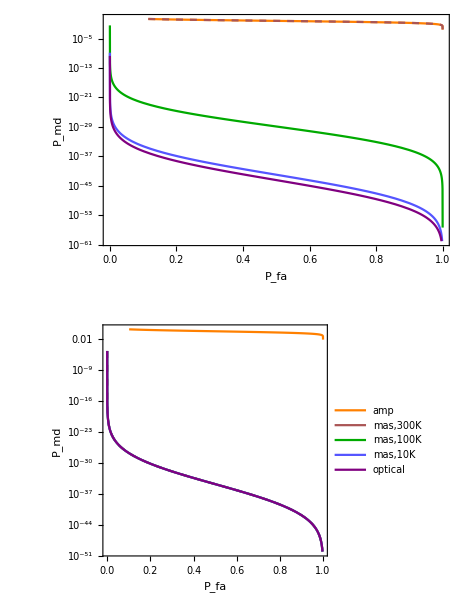

```mathematica
(*Homodyne detection - both symmetric and asymmetric cases*)
```

```mathematica
(*p0(x)*)
PDF[NormalDistribution[0,Sqrt[M λ0]],x]
```

(ⅇ^(-x^2/(2 M λ0)))/(√(2 π) √(M λ0))

```mathematica
Simplify[Integrate[(ⅇ^(-x^2/(2 M λ0)))/(√(2 π) √(M λ0)),{x,x0,Infinity}],M >0&&λ0>0 ]
```

```mathematica
Pfalse=1/2 (1-Erf[x0/(√2 √(M λ0))])
```

1/2 (1-Erf[x0/(√2 √(M λ0))])

```mathematica
(*p1(x)*)
PDF[NormalDistribution[M Sqrt[2 k Ns],Sqrt[M λ1]],x]
```

(ⅇ^(-(-√2 M √(k Ns)+x)^2/(2 M λ1)))/(√(2 π) √(M λ1))

```mathematica
Simplify[Integrate[(ⅇ^(-(-√2 M √(k Ns)+x)^2/(2 M λ1)))/(√(2 π) √(M λ1)),{x,-Infinity,x0}],M >0&&λ1>0&&Ns>0 ]
```

(√(2 k M^2 Ns-2 √2 M √(k Ns) x0+x0^2)+(-√2 M √(k Ns)+x0) Erf[(√((2 k M^2 Ns-2 √2 M √(k Ns) x0+x0^2)/(M λ1)))/(√2)])/(2 √(2 k M^2 Ns+x0 (-2 √2 M √(k Ns)+x0)))

```mathematica
Pmiss=1/2 (1- Erf[(√2 M √(k Ns)-x0)/(√2 √(M λ1))])
```

1/2 (1-Erf[(√2 M √(k Ns)-x0)/(√2 √(M λ1))])

```mathematica
λ1=.
```

```mathematica
PDF[NormalDistribution[M Sqrt[k Ns],Sqrt[M λ1]],x]
```

(ⅇ^(-(-M √(k Ns)+x)^2/(2 M λ1)))/(√(2 π) √(M λ1))

```mathematica
Simplify[Integrate[(ⅇ^(-(-M √(k Ns)+x)^2/(2 M λ1)))/(√(2 π) √(M λ1)),{x,-Infinity,x0}],M >0&&λ1>0&&Ns>0 ]
```

1/2 (1-((M √(k Ns)-x0) Erf[(√((-M √(k Ns)+x0)^2/(M λ1)))/(√2)])/(√((-M √(k Ns)+x0)^2)))

```mathematica
(*Recovering the usual total error probability for equal variances*)
FullSimplify[((Pfalse/.{λ0-> λ1})+Pmiss)/2/.{x0-> M Sqrt[2 k Ns]/2},M >0&&λ1>0&&Ns>0&&k>0]
```

1/2 Erfc[1/2 √((k M Ns)/λ1)]

```mathematica
Pmiss
```

1/2 (1-Erf[(√2 M √(k Ns)-x0)/(√2 √(M (1/2+k Na+Nb)))])

```mathematica
Pmiss/.{λ1-> k Na + Nb + 1/2}
```

```mathematica
PmissAmp=1/2 (1-Erf[(√2 M √(k Ns)-x0)/(√2 √(M (1/2+k Na+Nb)))])
```

1/2 (1-Erf[(√2 M √(k Ns)-x0)/(√2 √(M (1/2+k Na+Nb)))])

```mathematica
Pmiss/.{λ1-> k Nt + Nb + 1/2}
```

```mathematica
PmissRT=1/2 (1-Erf[(√2 M √(k Ns)-x0)/(√2 √(M (1/2+Nb+k Nt)))])
```

1/2 (1-Erf[(√2 M √(k Ns)-x0)/(√2 √(M (1/2+Nb+k Nt)))])

```mathematica
PmissRT/.Solve[(PfalseAmp/.{M->Mnu})==pf,x0]
```

```mathematica
Pfalse/.{λ0->  Nb + 1/2}
```

1/2 (1-Erf[x0/(√2 √(M (1/2+Nb)))])

```mathematica
PfalseAmp=1/2 (1-Erf[x0/(√2 √(M (1/2+Nb)))])
```

1/2 (1-Erf[x0/(√2 √(M (1/2+Nb)))])

```mathematica
PmissAmp
```

1/2 (1-Erf[(√2 M √(k Ns)-x0)/(√2 √(M (1/2+k Na+Nb)))])

```mathematica
PmissAmp/.Solve[(PfalseAmp/.{M->Mnu})==pf,x0]
```

```mathematica
PmissAmpNu[Ns_,Nb_,k_,Na_,M_,pf_]:=1/2 (1-Erf[(√2 M √(k Ns)-√M √(1+2 Nb) InverseErf[1-2 pf])/(√2 √(M (1/2+k Na+Nb)))])
```

```mathematica
PmissRTNu[Ns_,Nb_,k_,Nt_,f_,M_,pf_]:=1/2 (1-Erf[(√2 M √(k f Ns)-√M √(1+2 Nb) InverseErf[1-2 pf])/(√2 √(M (1/2+k Nt+Nb)))])
```

```mathematica
PmissCSNu[Ns_,Nb_,k_,Na_,M_,pf_]:=1/2 (1-Erf[(√2 M √(k Ns)-√M √(1+2 Nb) InverseErf[1-2 pf])/(√2 √(M (1/2+Nb)))])
```

```mathematica
FullSimplify[Series[1/2 (1-Erf[(√2 M √(k Ns)-√M √(1+2 Nb) InverseErf[1-2 pf])/(√2 √(M (1/2+k Na+Nb)))]),{Nb,Infinity,1}],Reals]
```

(1-pf)-(ⅇ^(-InverseErf[1-2 pf]^2) √(k M Ns) √(1/Nb))/(√π)-(ⅇ^(-InverseErf[1-2 pf]^2) k (Na+2 M Ns) InverseErf[1-2 pf])/(2 √π Nb)+O[1/Nb]^(3/2)

```mathematica
FullSimplify[Series[1/2 (1-Erf[(√2 M √(k Ns)-√M √(1+2 Nb) InverseErf[1-2 pf])/(√2 √(M (1/2+Nb)))]),{Nb,Infinity,1}],Reals]
```

(1-pf)-(ⅇ^(-InverseErf[1-2 pf]^2) √(k M Ns) √(1/Nb))/(√π)-(ⅇ^(-InverseErf[1-2 pf]^2) k M Ns InverseErf[1-2 pf])/(√π Nb)+O[1/Nb]^(3/2)

```mathematica
Pmiss/.{λ1->  Nb + 1/2}
```

```mathematica
PmissCS=1/2 (1-Erf[(√2 M √(k Ns)-x0)/(√2 √(M (1/2+Nb)))])
```

1/2 (1-Erf[(√2 M √(k Ns)-x0)/(√2 √(M (1/2+Nb)))])

```mathematica
Pfalse/.{λ0->  Nb + 1/2}
```

1/2 (1-Erf[x0/(√2 √(M (1/2+Nb)))])

```mathematica
PfalseCS=1/2 (1-Erf[x0/(√2 √(M (1/2+Nb)))])
```

1/2 (1-Erf[x0/(√2 √(M (1/2+Nb)))])

```mathematica
PmissCS/.{Solve[(PfalseCS)==pf,x0]}
```

```mathematica
PmissCSNu[Ns_,Nb_,k_,Na_,M_,pf_]:=1/2 (1-Erf[(√2 M √(k Ns)-√M √(1+2 Nb) InverseErf[1-2 pf])/(√2 √(M (1/2+Nb)))])
```

```mathematica
(*PLOTS*)
```

```mathematica
t=300;
ν1=10^9;
ν2=10^15;
h=6.62606957 10^-34;
kb=1.3806488 10^-23;
c=299792458;
wave1=N[c/ν1]
wave2=N[c/ν2]
α1=(h c)/(wave1 kb t);
α2=(h c)/(wave2 kb t);
N[1/(Exp[α1]-1)]
N[1/(Exp[α2]-1)]
```

0.299792

2.99792×10^-7

6250.49

3.34069×10^-70

```mathematica
aR=0.1;
range=N[1/(4 π) √(aR/10^(-5))]
```

7.95775

```mathematica
NsNUM=1/100;
NbNUM= 6250;
MNUM=10^3;
kNUM=10^(-8);
NaNUM1=0;
NaNUM2 = NbNUM;
NaNUM3=5 10^8;
```

```mathematica
(*Na=0 Homodyne*)
listROCAmphom1=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissAmpNu[NsNUM,NbNUM,kNUM,NaNUM1,MNUM,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Nb Homodyne*)
listROCAmphom2=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissAmpNu[NsNUM,NbNUM,kNUM,NaNUM2,MNUM,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Exp Homodyne*)listROCAmphom3=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissAmpNu[NsNUM,NbNUM,kNUM,NaNUM3,MNUM,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];

(*comp for Na=0 CS + Homodyne*)
listROCCShom1=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissCSNu[NsNUM +NaNUM1,NbNUM,kNUM,NaNUM1,MNUM,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];

(*comp for Na=Nb CS + Homodyne*)
listROCCShom2=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissCSNu[NsNUM+NaNUM2,NbNUM,kNUM,NaNUM2,MNUM,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];

(*comp for Na=Exp CS + Homodyne*)
listROCCShom3=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissCSNu[NsNUM+NaNUM3,NbNUM,kNUM,NaNUM3,MNUM,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];
```

```mathematica
(*Room temperature source*)
(*Na=Nb Homodyne, T=10K*)
listROCRThom21=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM2-Ne)/(1/100),NbNUM,kNUM,Ne,1/100,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 10,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Exp Homodyne, T=10K*)listROCRThom31=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM3-Ne)/(1/100),NbNUM,kNUM,Ne,1/100,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 10,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}]; 

(*Na=Nb Homodyne, T=100K*)
listROCRThom22=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM2-Ne)/(1/100),NbNUM,kNUM,Ne,1/100,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 100,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Exp Homodyne, T=100K*)listROCRThom32=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM3-Ne)/(1/100),NbNUM,kNUM,Ne,1/100,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 100,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Nb Homodyne, T=300K*)
listROCRThom23=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM2-Ne)/(1/100),NbNUM,kNUM,Ne,1/100,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 300,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Exp Homodyne, T=300K*)listROCRThom33=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM3-Ne)/(1/100),NbNUM,kNUM,Ne,1/100,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 300,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}];
```

```mathematica
kNUM
```

1/100000000

```mathematica
kNUM2=1/10000;
MNUM2=10^5;
```

```mathematica
(*Na=0 Homodyne*)
listROCAmphomNEW1=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissAmpNu[NsNUM,NbNUM,kNUM2,NaNUM1,MNUM2,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Nb Homodyne*)
listROCAmphomNEW2=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissAmpNu[NsNUM,NbNUM,kNUM2,NaNUM2,MNUM2,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Exp Homodyne*)listROCAmphomNEW3=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissAmpNu[NsNUM,NbNUM,kNUM2,NaNUM3,MNUM2,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];

(*comp for Na=0 CS + Homodyne*)
listROCCShomNEW1=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissCSNu[NsNUM +NaNUM1,NbNUM,kNUM2,NaNUM1,MNUM2,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];

(*comp for Na=Nb CS + Homodyne*)
listROCCSNEW2=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissCSNu[NsNUM+NaNUM2,NbNUM,kNUM2,NaNUM2,MNUM2,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];

(*comp for Na=Exp CS + Homodyne*)
listROCCSNEW3=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissCSNu[NsNUM+NaNUM3,NbNUM,kNUM2,NaNUM3,MNUM2,pfa],100]]},{pfa,0.0000001,0.99999,0.001}];
```

```mathematica
(*Room temperature source*)
(*Na=Nb Homodyne, T=10K*)
listROCRThomNEW21=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM2-Ne)/(1/100),NbNUM,kNUM2,Ne,1/100,MNUM2,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 10,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Exp Homodyne, T=10K*)listROCRThomNEW31=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM3-Ne)/(1/100),NbNUM,kNUM2,Ne,1/100,MNUM2,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 10,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}]; 

(*Na=Nb Homodyne, T=100K*)
listROCRThomNEW22=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM2-Ne)/(1/100),NbNUM,kNUM2,Ne,1/100,MNUM2,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 100,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Exp Homodyne, T=100K*)listROCRThomNEW32=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM3-Ne)/(1/100),NbNUM,kNUM2,Ne,1/100,MNUM2,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 100,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Nb Homodyne, T=300K*)
listROCRThomNEW23=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM2-Ne)/(1/100),NbNUM,kNUM2,Ne,1/100,MNUM2,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 300,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}];

(*Na=Exp Homodyne, T=300K*)listROCRThomNEW33=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM3-Ne)/(1/100),NbNUM,kNUM2,Ne,1/100,MNUM2,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 300,f-> 1/100},100]]},{pfa,0.0000001,0.99999,0.001}];
```

```mathematica
ListLogPlot[{listROCRThomNEW22,listROCRThomNEW21,listROCCSNEW2},Joined->True,PlotRange-> {{0,1},{0,0.001}},Frame->True,FrameLabel->{{"P_md",""},{"P_fa",""}},PlotLegends->Placed[{"amp","300","100","10","optical"},{0.15,0.6}],PlotStyle->{Darker[Green],Lighter[Blue],Purple},PlotRange->Full,FrameTicks->{{{0.00001,0.0001,0.001},Automatic},Automatic}]
```

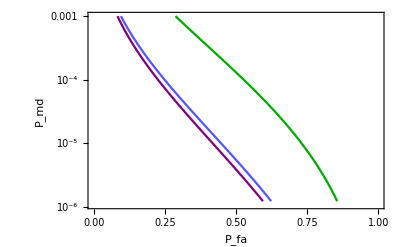

```mathematica
GraphicsColumn[{ListLogPlot[{listROCAmphomNEW2,Re[listROCRThomNEW23],listROCRThomNEW22,listROCRThomNEW21,listROCCSNEW2},Joined->True,PlotRange-> {{0,1},{0,1}},Frame->True,FrameLabel->{{"P_md",""},{"P_fa",""}},PlotLegends->Placed[{"amp","300","100","10","optical"},{0.15,0.6}],PlotStyle->{Orange,{Darker[Pink],Dashed},Darker[Green],Lighter[Blue],Purple}],
ListLogPlot[{listROCAmphom2,Re[listROCRThom23],listROCRThom22,listROCRThom21,listROCCShom2},Joined->True,PlotRange-> {{0,1},{0,1}},Frame->True,FrameLabel->{{"P_md",""},{"P_fa",""}},PlotLegends->Placed[{"amp","300","100","10","optical"},{0.15,0.6}],PlotStyle->{Orange,{Darker[Pink]},Darker[Green],Lighter[Blue],Purple}],
ListLogPlot[{listROCAmphom3,listROCRThom33,listROCRThom32,listROCRThom31,listROCCShom3},Joined->True,PlotRange-> {{0,1},{0,1}},Frame->True,FrameLabel->{{"P_md",""},{"P_fa",""}},PlotLegends->Placed[{"amp","300","100","10","optical"},{0.15,0.6}],PlotStyle->{Orange,{Darker[Pink]},Darker[Green],Lighter[Blue],Purple}]}]
```

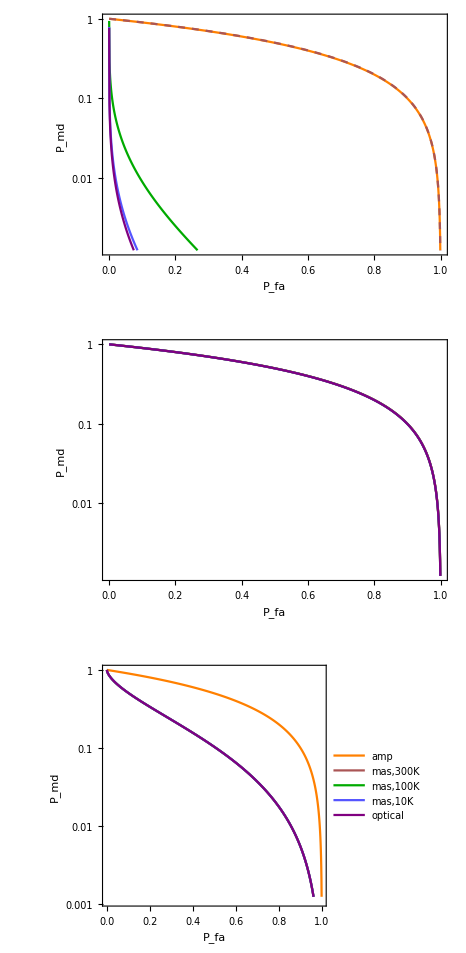

```mathematica
GraphicsColumn[{
ListLogPlot[{listROCAmphom2,Re[listROCRThom23],listROCRThom22,listROCRThom21,listROCCShom2},Joined->True,PlotRange-> {{0,1},{0,1}},Frame->True,FrameLabel->{{"P_md",""},{"P_fa",""}},PlotLegends->Placed[{"amp","300","100","10","optical"},{0.15,0.6}],PlotStyle->{Orange,{Darker[Pink]},Darker[Green],Lighter[Blue],Purple}],
ListLogPlot[{listROCAmphom3,Re[listROCRThom33],listROCRThom32,listROCRThom31,listROCCShom3},Joined->True,PlotRange-> {{0,1},{0,1}},Frame->True,FrameLabel->{{"P_md",""},{"P_fa",""}},PlotLegends->Placed[{"amp","300","100","10","optical"},{0.15,0.6}],PlotStyle->{Orange,{Darker[Pink]},Darker[Green],Lighter[Blue],Purple}]

}]
```

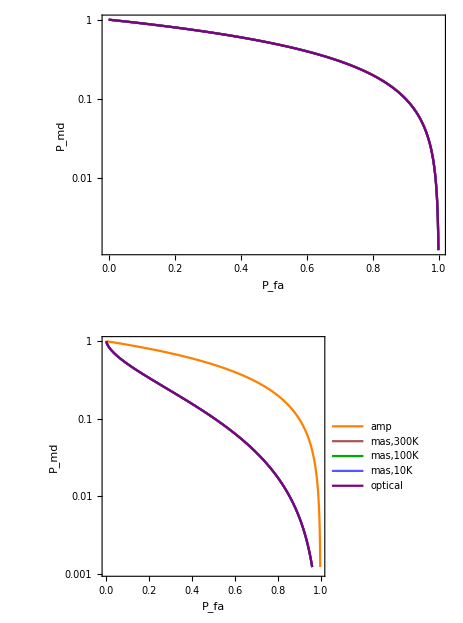

```mathematica
ListLogPlot[{listROCAmphom2,Re[listROCRThom23],listROCRThom22,listROCRThom21,listROCCShom2},Joined->True,PlotRange-> {{0.82,0.823},{0.176,0.18}},Frame->True,FrameLabel->{{"P_md",""},{"P_fa",""}},PlotLegends->Placed[{"amp","300","100","10","optical"},{0.15,0.6}],PlotStyle->{Orange,{Darker[Pink],Dashed},Darker[Green],Lighter[Blue],Purple},FrameTicks->{Automatic,{{0.8205, 0.8215,0.8225},{None}}}]
```

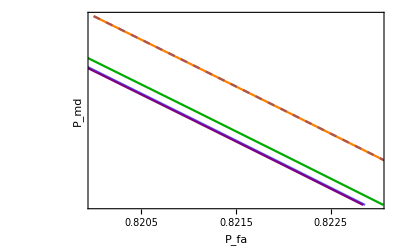

```mathematica
(*Room temperature source*)
(*RT Homodyne, T=0.1K*)
listROChomRT01=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM2-Ne)/(1/100),NbNUM,1/100,Ne,1/100,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 1/10,f-> 1},100]]},{pfa,0.0000001,0.99999,0.001}];
(*CS Homodyne, T=0.1K*)listROChomCS01=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissCSNu[(NsNUM+NaNUM3-Ne)/(1/100),NbNUM,1/100,Ne,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 1/10,f-> 1},100]]},{pfa,0.0000001,0.99999,0.001}]; 

(*TMSV Homodyne, T=0.1K*)
listROChomTMSV01=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM2-Ne)/(1/100),NbNUM,1/100,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 1/10,f-> 1},100]]},{pfa,0.0000001,0.99999,0.001}];
(*RT Homodyne, T=0.001K*)
listROChomRT0001=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM2-Ne)/(1/100),NbNUM,1/100,Ne,1,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 1/1000,f-> 1},100]]},{pfa,0.0000001,0.99999,0.001}];
(*CS Homodyne, T=0.001K*)listROChomCS0001=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissCSNu[(NsNUM+NaNUM3-Ne)/(1/100),NbNUM,1/100,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 1/1000,f-> 1},100]]},{pfa,0.0000001,0.99999,0.001}]; 

(*TMSV Homodyne, T=0.001K*)
listROChomTMSV0001=Table[{pfa,Block[{$MaxExtraPrecision=1000},N[PmissRTNu[(NsNUM+NaNUM2-Ne)/(1/100),NbNUM,kNUM,MNUM,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 1/1000,f->1},100]]},{pfa,0.0000001,0.99999,0.001}];
```

```mathematica
GraphicsColumn[{Plot[{(1/2)RTChern^(10^M)/.{k->1/100,Ns-> (1/100)/f,f-> 1/100}/.{v-> 10^9,Nb-> 6250,T-> 1/10,f-> 1/100},(1/2)CSChern^(10^M)/.{Nb-> 6250,k-> 1/100,Ns-> 1/100+Ne}/.{v-> 10^9,Nb-> 6250,T-> 1/10,f-> 1/100},(1/2)N[TMSVampQCB[1/100+Ne,6250,1/100,0,0]/.{v-> 10^9,Nb-> 6250,T-> 1/10}]^(10^M)},{M,3,8},PlotStyle->{Lighter[Orange],Purple,Lighter[Red]},Frame->True,FrameLabel->{"Log_10(M)","P_err"}],Plot[{(1/2)RTChern^(10^M)/.{k->1/100,Ns-> (1/100)/f,f-> 1/100}/.{v-> 10^9,Nb-> 6250,T-> 1/100,f-> 1/100},(1/2)CSChern^(10^M)/.{Nb-> 6250,k-> 1/100,Ns-> 1/100+Ne}/.{v-> 10^9,Nb-> 6250,T-> 1/100,f-> 1/100},(1/2)N[TMSVampQCB[1/100+Ne,6250,1/100,0,0]/.{v-> 10^9,Nb-> 6250,T-> 1/100}]^(10^M)},{M,3,8},PlotLegends->Placed[{"mas, T K","optical","TMSV"},{0.85,0.7}],PlotStyle->{Lighter[Orange],Purple,Lighter[Red ]},Frame->True,FrameLabel->{"Log_10(M)","P_err"}],Plot[{(1/2)RTChern^(10^M)/.{k->1/100,Ns-> (1/100)/f,f-> 1/100}/.{v-> 10^9,Nb-> 6250,T-> 1/1000,f-> 1/100},(1/2)CSChern^(10^M)/.{Nb-> 6250,k-> 1/100,Ns-> 1/100+Ne}/.{v-> 10^9,Nb-> 6250,T-> 1/1000,f-> 1/100},(1/2)N[TMSVampQCB[1/100+Ne,6250,1/100,0,0]/.{v-> 10^9,Nb-> 6250,T-> 1/1000}]^(10^M)},{M,3,8},PlotStyle->{Lighter[Orange],{Purple,Dashed},Lighter[Red]},Frame->True,FrameLabel->{"Log_10(M)","P_err"}]}]
```

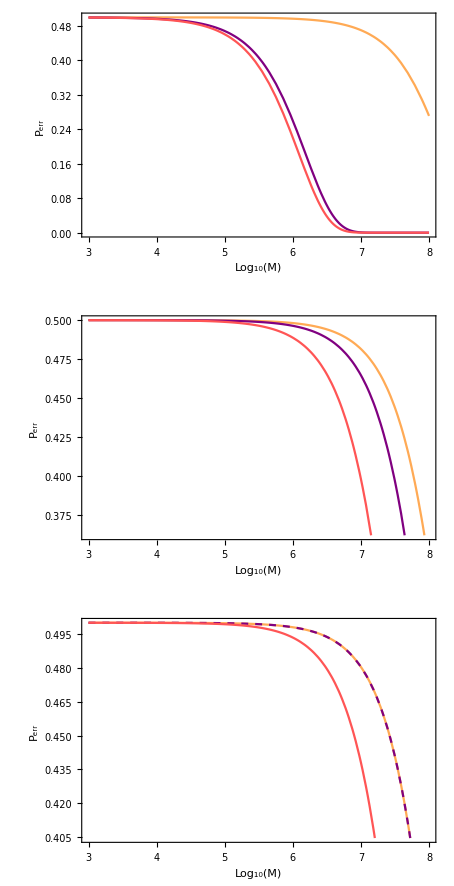

```mathematica
Ne/.{v-> 10^9,Nb-> 6250,T-> 1/1000,f-> 1/100}
Ne/.{v-> 10^9,Nb-> 6250,T-> 1/100,f-> 1/100}
Ne/.{v-> 10^9,Nb-> 6250,T-> 1/10,f-> 1/100}
Ne/.{v-> 10^9,Nb-> 6250,T-> 10,f-> 1/100}
```

1.43599×10^-21

0.00830437

1.6235

207.867

```mathematica
NbNUM=6250;
```

```mathematica
GraphicsColumn[{LogPlot[{TypeIIErrRT[1/100,NbNUM,1/100,Ne,1,1000000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 1/10,f-> 1},TypeIIErrCS[1/100+Ne,NbNUM,1/100,1000000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 1/10,f-> 1},TypeIIErrTMSV[1/100+Ne,6250,1/100,1000000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 1/10,f-> 1}},{pfa,0,1},PlotRange->{{0,1},{10^(-5),1.2}},Frame->True,PlotLegends->Placed[{"mas, T K","optical","TMSV"},{0.85,0.7}],FrameLabel->{"P_fa","P_md"},PlotStyle->{Lighter[Orange],{Purple},{Lighter[Red]}}],
LogPlot[{TypeIIErrRT[1/100,NbNUM,1/100,Ne,1,100000000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 0.001,f-> 1},TypeIIErrCS[1/100+Ne,NbNUM,1/100,100000000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 0.001,f-> 1},TypeIIErrTMSV[1/100+Ne,6250,1/100,100000000,pfa]/.{v-> 10^9,Nb-> NbNUM,T-> 0.001,f-> 1}},{pfa,0,1},PlotRange->{{0,1},{10^(-10),1.2}},Frame->True,FrameLabel->{"P_fa","P_md"},PlotStyle->{Lighter[Orange],{Purple,Dashed},{Lighter[Red]}},PlotLegends->Placed[{"mas, T K","optical","TMSV"},{0.85,0.7}]]
}]
```